```mathematica
(*with height one, angle is sin(hal aperture)*)
na = 1.35
n = 1.404
na2=0.95
n2=1
g1 =Graphics3D[Cone[{{0,0,1},{0,0,0}},na / n]]
g2 = Graphics3D[Cone[{{0,0,1},{0,0,0}},na2 / n2]]

Show[g1,g2]
```

1.35

1.404

0.95

1

-Graphics3D-

-Graphics3D-

-Graphics3D-

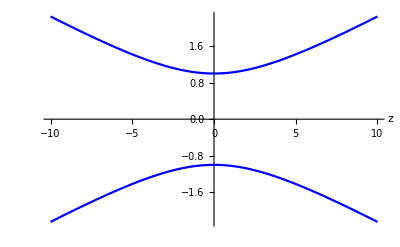

```mathematica
(*Define parameters*)
w0=1(*Beam waist*)
lambda=0.6328(*Wavelength*)
n=1(*Index of refraction*)
(*Define the Gaussian beam radius function*)w[z_]:=w0*Sqrt[1+(lambda*z/(Pi*w0^2*n))^2];

P = 10
(*Define the radial dependence of pulse irradiance*)irradiance[r_,z_]:=(2 *P / Pi* w[z])*Exp[-2 r^2/w[z]^2];

(*a / (h u)=1*)
hbar =10^-34
ruse=1
N1P [z_]= Exp[-hbar *w[z]]*irradiance[ruse,z]

(*b/2hu = 1*)
N2P [z_]= irradiance[ruse,z] / (1 + irradiance

(*Plot the beam radius as a function of z*)
Plot[{w[z],-w[z]},{z,-10,10},AxesLabel->{"z",None},PlotStyle->{Blue},GridLines->None,(*Remove the grid lines*)TicksStyle->White  (*Set tick color to white to hide them*)]
```

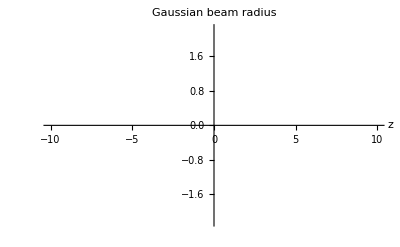

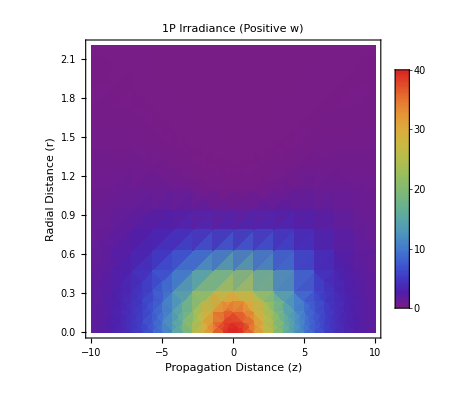

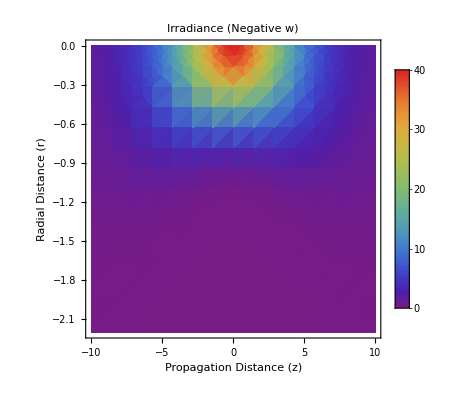

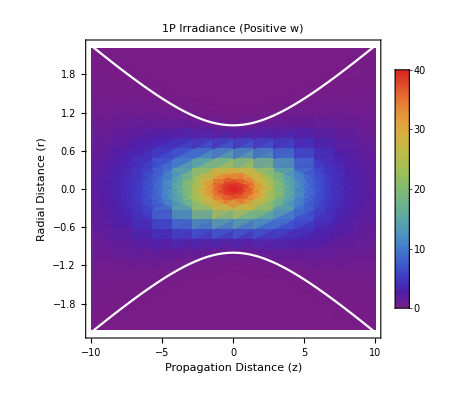

```mathematica
(*Define parameters*)w0=1;(*Beam waist*)lambda=0.6328;(*Wavelength*)n=1;(*Index of refraction*)P=10;
hbar = 10^(-34);
(*Power*)(*Define the Gaussian beam radius function*)w[z_]:=w0*Sqrt[1+(lambda*z/(Pi*w0^2*n))^2]/. Pi->N[Pi];

(*Define the radial dependence of pulse irradiance*)
irradiance[r_,z_]:=(2*P/(Pi*(w[z])^2))*Exp[-2 r^2/(w[z])^2];

photon1[r_,z_] = Exp[-hbar*w[z]*z]*irradiance[r,z];  

b[z_]= 2*hbar*w[z];
photon2[r_,z_] = (irradiance[r,z] / (1 + b[z]*z*irradiance[r,z]))^2;

(*Plot Gaussian beam radius on w x z plane*)
plot1 = Plot[{w[z],-w[z]},{z,-10,10},PlotStyle->White, AxesLabel->{"z",None},PlotStyle->{Blue},GridLines->None,(*Remove the grid lines*)TicksStyle->White ,
PlotLabel->"Gaussian beam radius"(*Set tick color to white to hide them*)]

(*Overlay irradiance as a color map for positive values of w*)plot2 = DensityPlot[photon2[r,z],{z,-10,10},{r,0,2.2},AxesLabel->{"Propagation Distance (z)","Radial Distance (r)"},PlotLabel->"1P Irradiance (Positive w)",ColorFunction->"Rainbow",(*Adjust the color map as needed*)PlotLegends->Automatic,PlotRange->All,FrameTicks->{{Automatic,None},{Automatic,None}}]

(*Overlay irradiance as a color map for negative values of w*)
plot3 = DensityPlot[photon2[r,z],{z,-10,10},{r,0,-2.2},AxesLabel->{"Propagation Distance (z)","Radial Distance (r)"},PlotLabel->"Irradiance (Negative w)",ColorFunction->"Rainbow",(*Adjust the color map as needed*)PlotLegends->Automatic,PlotRange->All,FrameTicks->{{Automatic,None},{Automatic,None}}]

(*Overlay the curve of w[z] on the plots*)
Show[plot2,plot3,plot1, PlotRange->All]
```